```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Constants*)
(*Atomic Units*)
m:=1
e:=1
ℏ:=1
ke:=1
k:=1
```

## Double Finite Wall Infinite Well Potential

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Constants*)
(*Atomic Units*)
m:=1
e:=1
ℏ:=1
ke:=1
k:=1
```

```mathematica
(*Parameters*)
a:=10
V0:=1
```

```mathematica
(*Potential Energy*)
V[x_]=Piecewise[{{V0,a/5≤x≤2 a/5},{V0,3 a/5≤x≤4 a/5}},0];
```

```mathematica
(*Schrodinger Equation*)
TISE=ϵ ψ[x]==-ℏ^2 ψ''[x]/(2 m)+V[x]ψ[x];
```

```mathematica
(*a=10*)
ϵ1:=0.3885
ϵ2:=0.6204
ϵ3:=0.6475
ϵ4:=1.276
```

```mathematica
sol=NDSolve[{TISE/.ϵ->ϵ2,ψ[0]==0,ψ'[0]==0.1},ψ,{x,0,a}]
sol=Evaluate[First[ψ[x]/.%]]
```

{{ψ→InterpolatingFunction[…]}}

InterpolatingFunction[…][x]

```mathematica
norm=Integrate[Conjugate[sol] sol,{x,0,a}];
solnormed=sol/norm//N
```

39.0115 InterpolatingFunction[…][x]

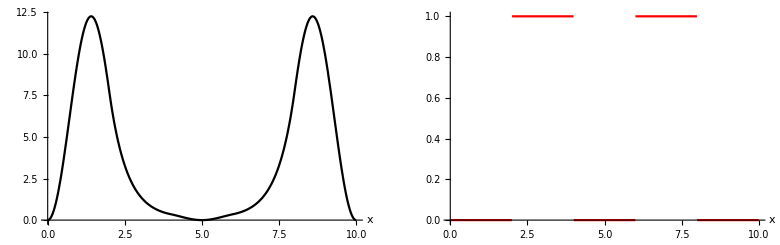

```mathematica
wave=Plot[solnormed^2,{x,0,a},Axes->True,AxesLabel->Automatic,PlotStyle->Black,ImageSize->Medium];
potential=Plot[V[x],{x,0,a},Axes->True,AxesLabel->Automatic,PlotStyle->Red,ImageSize->Medium];
GraphicsRow[{wave,potential}]
```

## Finite Square Well Potential

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Constants*)
(*Atomic Units*)
m:=1
e:=1
ℏ:=1
ke:=1
k:=1
```

```mathematica
(*Parameters*)
a:=1
A:=5
V0:=10
```

```mathematica
(*Potential Energy*)
V[x_]=Piecewise[{{0,0≤x≤a}},V0];
```

```mathematica
(*Schrodinger Equation*)
TISE=ϵ ψ[x]==-ℏ^2 ψ''[x]/(2 m)+V[x] ψ[x];
```

```mathematica
ϵ1:=0.702
ϵ2:=19.8
ϵ3:=44.3
ϵ4:=78.8
```

```mathematica
NDSolve[{TISE/.ϵ->8.17899,ψ[-A/2]==0,ψ'[-A/2]==0.00000001},ψ,{x,-A/2,a+A/2}];
sol=Evaluate[First[ψ[x]/.%]];
```

```mathematica
norm=Integrate[Conjugate[sol] sol,{x,-A/2,a+A/2}];
solnormed=sol/norm//N;
```

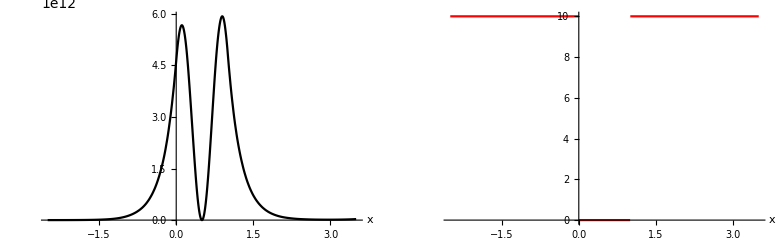

```mathematica
wave=Plot[solnormed^2,{x,-A/2,a+A/2},Axes->True,AxesLabel->Automatic,PlotStyle->Black,ImageSize->Medium];
potential=Plot[V[x],{x,-A/2,a+A/2},Axes->True,AxesLabel->Automatic,PlotStyle->Red,ImageSize->Medium];
GraphicsRow[{wave,potential}]
```